```mathematica
(*Solve dy/dx = sin(x-y) : Plot Direction Field : Plot Solution Curves*)
```

```mathematica
de = y'[x] == Sin[x - y[x]];
```

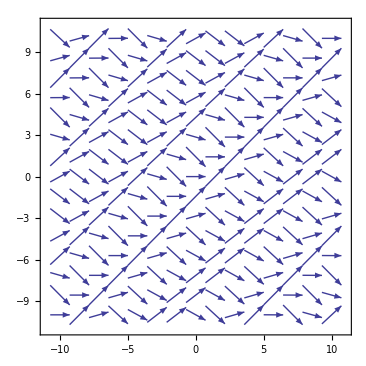

```mathematica
VectorPlot[{1,Sin[x-y]}, {x, -10, 10}, {y, -10, 10}]
```

```mathematica
(*Plot Solution Curve*)
```

```mathematica
soln1  = DSolve[{de, y[1] == 0}, y[x], x];
```

```mathematica
T1 = Table[y[x]/.soln1[[k]], {k,4}];
```

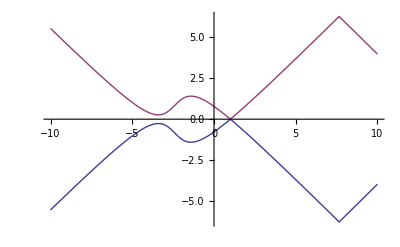

```mathematica
P1 =Plot[T1, {x, -10, 10}]
soln2 = DSolve[{de, y[1] == 3}, y[x], x];
```

```mathematica
soln3  = DSolve[{de, y[3] == 0}, y[x], x];
```

```mathematica
soln4  = DSolve[{de, y[3] == 31}, y[x], x];
```

```mathematica
T2 = Table[y[x]/.soln2[[k]], {k,4}];
```

```mathematica
T3 = Table[y[x]/.soln3[[k]], {k,4}];
```

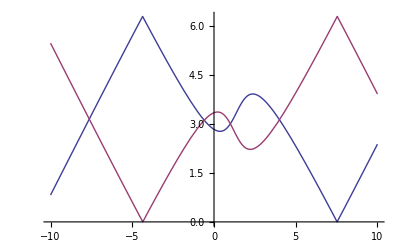

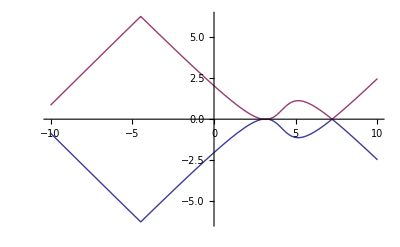

```mathematica
P2 =Plot[T2, {x, -10, 10}]
P3 =Plot[T3, {x, -10, 10}]
```

```mathematica
P4 =Plot[T4, {x, -10, 10}]
```

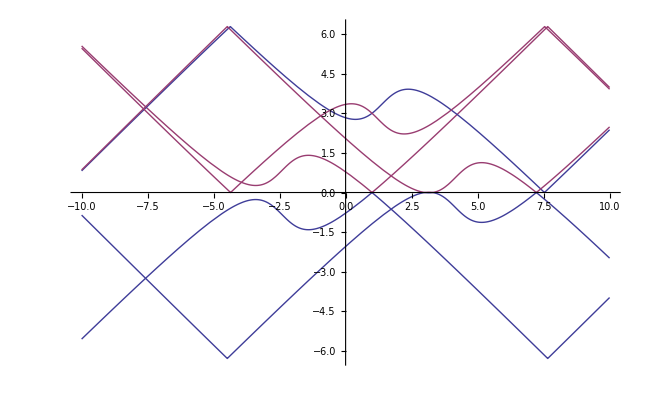

```mathematica
Show[P1,P2, P3, P4]
```